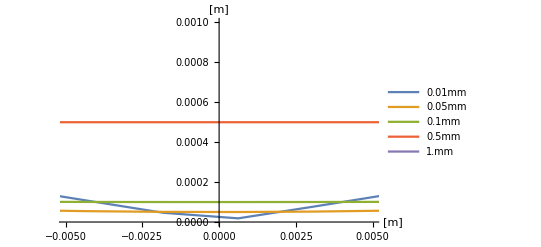

```mathematica
waists = {10^-5,5*10^-5,10^-4,5*10^-4,10^-3};
leg = Table[StringForm["``mm",w/10^-3//N],{w,waists}];
Plot[Evaluate[Table[w0 √(1+z^2/((π w0^2)/(7.8*^-7))^2),{w0,waists}]],{z,-π*0.001^2/(7.8*^-7),π*0.001^2/(7.8*^-7)},PlotRange->{{-.005,.005},{0,0.001}},PlotLegends->leg,AxesLabel->{"[m]","[m]"}]
```